## 1.6.1

Convert to polar from (give r=abs(z) and θ=arg(z)). Do: c, e, h, j

c) abs(((1+ⅈ)/(√2))^4).
The magnitude of the interior is |(1+ⅈ)/(√2)|=√(1/2+1/2)=1.  The argument is arctan(1)=π/4.
The magnitude is 1^4 the argument is 4*π/4=π.  The thing simplifies to -1!

```mathematica
Simplify[((1+ⅈ)/(√2))^4]
```

-1

e) The roots of z^8==-1=1 ⅇ^(-π ⅈ).  The roots are z_k=1^(1/8)ⅇ^(-k π/8 ⅈ) for k=0,1,2,3,4,5,6,7. At k=8 the roots repeat.
The magnitude of each root is r=1.  The arguments of the kth root is θ_k=k π/8.

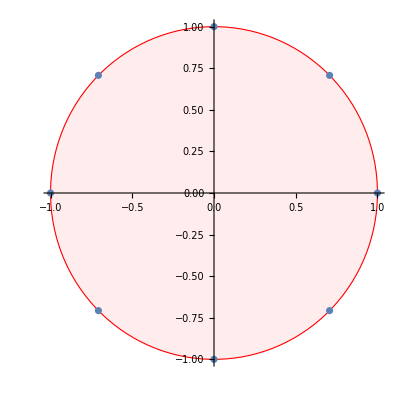

```mathematica
ListPlot[ReIm[z/.Solve[z^8==1,z]],
AspectRatio->Automatic,
Prolog->{LightPink,EdgeForm[Red],Disk[{0,0},1]}]
```

h) z=(1+ⅈ)/(1+ⅈ √3)=(1+ⅈ)/(1+ⅈ √3)(1-ⅈ √3)/(1-ⅈ √3)=((1+ⅈ)(1-ⅈ √3))/(1+3)=((1+ⅈ)+(1-ⅈ) √3)/4=((1+√3)+ⅈ (1-√3))/4.
The magnitude is 
1/4 √((1+√3)^2+(1-√3)^2)=1/4 √((1+2 √3+9)+(1-2 √3+9))=(√8)/4=1/(√2)≈0.7071
The argument is aTan((1-√3)/(1+√3))≈-0.2618

```mathematica
z=(1+ⅈ)/(1+ⅈ √3);
{AbsArg[z],AbsArg[1.0z]}
```

{{1/(√2),ArcTan[(1/4-(√3)/4)/(1/4+(√3)/4)]},{0.707107,-0.261799}}

j) z=ⅈ^(ⅈ/2)=(ⅇ^(-ⅈ π/2))^(ⅈ/2)=ⅇ^(-ⅈ π/2 ⅈ/2)=ⅇ^(-π /4)≈0.4559 
arg(z) = 0 and abs(z) ≈0.4559

```mathematica
z=ⅈ^(ⅈ/2);
{AbsArg[z],AbsArg[1.0z]}
```

{{ⅇ^(-π/4),0},{0.455938,0.}}

## 1.6.2

Convert to a+b ⅈ form. Do: a, e, i

a) 1/(6+2ⅈ)=1/(6+2ⅈ)(6-2ⅈ)/(6-2ⅈ)=(6-2ⅈ)/(36+4)=6/40-2/40 i=3/20-1/20 i

```mathematica
z=1/(6+2ⅈ);
ReIm[z]
```

{3/20,-1/20}

e) The roots of z^5=2=2 ⅇ^(k 2π ⅈ) for any k.  The roots are 
	z_k=2^(1/5)ⅇ^((k 2π)/5 ⅈ)=2^(1/5)(cos((k 2π)/5)+ⅈ sin((k 2π)/5)) 
for k=0,1,2,3,4.  Roots repeat for k=5,6,7,…

i) z=((1-ⅈ √3)/(2+2ⅈ))^2=((1-ⅈ √3)/(2+2ⅈ)(2-2ⅈ)/(2-2ⅈ))^2=(((1-ⅈ √3)(2-2ⅈ))/(4+4))^2
z=1/8^2((2-2 √3)+ⅈ(-2-2 √3))^2
z=1/64(16 ⅈ-16 √3)
The imaginary part is 16/64=1/4.  The real part is -16√3/64=-(√3)/4.

```mathematica
z=((1-ⅈ √3)/(2+2ⅈ))^2;
ReIm[z]
```

{-(√3)/4,1/4}

## 1.6.3

Assume 
	z_0^n+a_1 z_0^(n-1)+a_2 z_0^(n-2)+…+a_(n-1)z_0^1+a_n=0
and that all the a_k are real i.e. (ā)_k=a_k then
	OverBar[z_0^n+a_1 z_0^(n-1)+a_2 z_0^(n-2)+…+a_(n-1)z_0^1+a_n]=OverBar[0]
so
	OverBar[z_0^n]+OverBar[a_1 z_0^(n-1)]+OverBar[a_2 z_0^(n-2)]+…+OverBar[a_(n-1)z_0^1]+(ā)_n=0
so 
	OverBar[z_0^n]+(ā)_1 OverBar[z_0^(n-1)]+(ā)_2 OverBar[z_0^(n-2)]+…+(ā)_(n-1)OverBar[z_0^1]+(ā)_n=0
so 
	(z̄)_0^n+a_1(z̄)_0^(n-1)+a_2(z̄)_0^(n-2)+…+a_(n-1)(z̄)_0+a_n=0.
In words,  if z_0 is a root of a real polynomial then so is its complex conjugate.  
In other words, roots of real polynomials are either real or come in complex conjugate pairs.

{-0.728769-0.434072 ⅈ,-0.728769+0.434072 ⅈ,-0.291038-1.09885 ⅈ,-0.291038+1.09885 ⅈ,0.236918-0.5953 ⅈ,0.236918+0.5953 ⅈ,1.17145,3.72766}

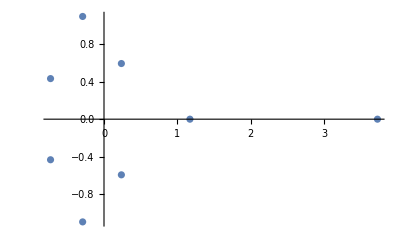

```mathematica
Clear[z]
p[z_]= Sum[RandomInteger[{-10,10}] z^i,{i,0,8}];
roots=NSolveValues[p[z]==0,z]
ListPlot[ReIm[roots]]
```